# Oscilador armónico cuántico usando derivadas generales conformables

## Oscilador armónico cuántico

#### Parámetros

```mathematica
l = 1;
hbar =1;
omega= 1;
m = 1;
```

#### Función de onda

```mathematica
Ps[n_,x_]:=1/Sqrt[2^n n!] (m* omega/Pi *hbar)^(1/4) Exp[-(m *omega *x^2)/(2 *hbar)] HermiteH[n,Sqrt[(m* omega)/hbar] x];
```

```mathematica
Funmod[p_]:=Abs[p]^2;
```

#### Potencial

```mathematica
V[x_]:=0.5 m omega^2 x^2
```

#### Gráficas

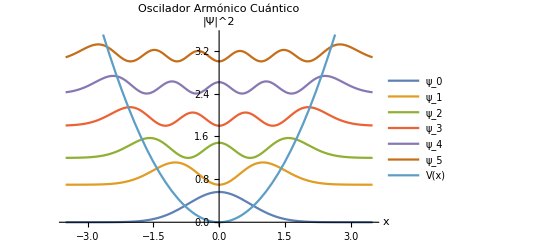

```mathematica
Plot[{Funmod[Ps[0,x]],Funmod[Ps[1,x]]+0.7,Funmod[Ps[2,x]]+1.2,Funmod[Ps[3,x]]+1.8,Funmod[Ps[4,x]]+2.4,Funmod[Ps[5,x]]+3,V[x]},{x,-3.5,3.5},PlotRange->{0,3.5},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},AxesLabel->{"x","|Ψ|^2"},PlotLabel->"Oscilador Armónico Cuántico"]
```

## Simulaciones Jafarov

### Simétrico

#### Parámetros

```mathematica
a = 3;
b = 3;
l = 1;
w = 1;
```

#### Potencial

```mathematica
m=b*a/((a+x)*(b-x));
V = (m*w^2*x^2)/2;
```

#### Constantes de normalización

```mathematica
C0= (a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 *0+2^2 a*b+1)*Gamma[2 *0+2^2 a*b+1]*Factorial[0]/(Gamma[0+2*l^2*(a^2*b/(a+b))+1]*Gamma[0+2*l^2*(a^2*b/(a+b))+1])];
C1 = (a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 1+2^2 a*b+1)*Gamma[2 1+2^2 a*b+1]*Factorial[1]/(Gamma[1+2*l^2*(a^2*b/(a+b))+1]*Gamma[1+2*l^2*(a^2*b/(a+b))+1])];
C2=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 2+2^2 a*b+1)*Gamma[2 2+2^2 a*b+1]*Factorial[2]/(Gamma[2+2*l^2*(a^2*b/(a+b))+1]*Gamma[2+2*l^2*(a^2*b/(a+b))+1])];
C3=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 3+2^2 a*b+1)*Gamma[2 3+2^2 a*b+1]*Factorial[3]/(Gamma[3+2*l^2*(a^2*b/(a+b))+1]*Gamma[3+2*l^2*(a^2*b/(a+b))+1])];
c4=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 4+2^2 a*b+1)*Gamma[2 4+2^2 a*b+1]*Factorial[4]/(Gamma[4+2*l^2*(a^2*b/(a+b))+1]*Gamma[4+2*l^2*(a^2*b/(a+b))+1])];
c5=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 5+2^2 a*b+1)*Gamma[2 5+2^2 a*b+1]*Factorial[5]/(Gamma[5+2*l^2*(a^2*b/(a+b))+1]*Gamma[5+2*l^2*(a^2*b/(a+b))+1])];
```

#### Funciones de onda

```mathematica
Ps0[x_] := C0*(a+x)^(l^2*(a^2*b/(a+b))) *(b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[0,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi1[x_] :=C1*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[1,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi2[x_]:=C2*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[2,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi3[x_]:=C3*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[3,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi4[x_]:=c4*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[4,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi5[x_]:=c5*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[5,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Funmod[p_]:= Abs[p]^2;
```

SetDelayed::write: Tag Times in ((10 ⅇ^(-(50 ⅇ^(9/10 «1»))/(9 (2+Times[«2»]) (5+x))) x)/((2-x) (5+x))-ⅇ^(-(9 x^2)/10-(50 ⅇ^Times[«2»])/(9 Plus[«2»] Plus[«2»])) ((50 ⅇ^(9/10 Power[«2»]))/(9 (2+Times[«2»]) (5+x)^2)-(50 ⅇ^(9/10 Power[«2»]))/(9 (2+Times[«2»])^2 (5+x))-(10 ⅇ^(9/10 Power[«2»]) x)/((2+Times[«2»]) (5+x))))/(2 √5 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√5 x ((10 ⅇ^(-50/9 Power[«1»] «1» Power[«2»]) x)/((2+Times[«2»]) (5+x))-ⅇ^(Times[«2»]+Times[«4»]) (50/9 Power[«2»] Power[«2»] Power[«2»]-«1»-10 «3» Power[«2»])))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«1»])«1»(«1»«1»)/(4 √5 («1»)^(3/2))+(«1»+«1»+«6»)/(2 √5 «1»)))/(2 √10 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/2) x ((√5 x (10 Power[«2»] Power[«2»] x Power[«2»]-Power[«2»] Plus[«1»]))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10«1»«5»«1»«1»]) («1»+«1»)))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«2»]) («1»))/(4 √10 (Power[«2»] «1»)^(3/2))+(«1»)/(2 √10 √(«1» «1»))))/(2 √30 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/6) x ((√(5/2) x (Power[«2»] Power[«2»] x Power[«1»] Power[«2»] Plus[«2»]-«1»))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10 «1») (-1/4 «4»+1/2 «3»)))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«2»]) («1»))/(4 √30 (Power[«2»] «1»)^(3/2))+(«1»)/(2 √30 √(«1» «1»))))/(4 √30 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/6) x ((√(5/6) x (Power[«2»] Power[«2»] x Power[«1»] Power[«2»] Plus[«2»]-«1»))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10 «1») (-1/4 «4»+1/2 «3»)))/(2 (2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«1»]) («1»))/(8 √30 (Power[«2»] «1»)^(3/2))+(-«1» «5»+«8»)/(4 √30 √(«1»))))/(20 √6 √(1/((2-x) (5+x))))[x_] is Protected.

#### Gráficas

General::munfl: Exp[-1828.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1837.08] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-924.439] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

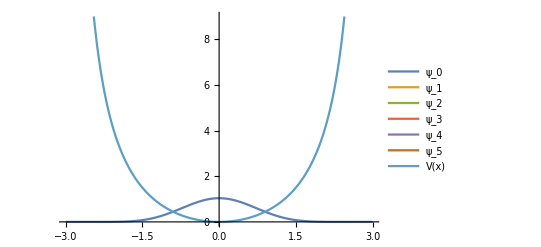

```mathematica
Plot[{Funmod[Ps0[x]/(8*10^12)],Funmod[Psi1[x]/(6*10^13)]+1.2,Funmod[Psi2[x]/(4*10^14)]+2.4,Funmod[Psi3[x]/(4*10^15)]+4.2,Funmod[Psi4[x]/(4*10^16)]+5.7,Funmod[Psi5[x]/(4*10^17)]+7.1,V},{x,-3,3},PlotRange->{0,9},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"}]
```

### Asimétrico izquierda

#### Parámetros

```mathematica
a = 2;
b = 5;
l = 1;
w = 1;
```

#### Potencial

```mathematica
m=b*a/((a+x)*(b-x));
V = (m*w^2*x^2)/2;
```

#### Constantes de normalización

```mathematica
C0= (a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 *0+2^2 a*b+1)*Gamma[2 *0+2^2 a*b+1]*Factorial[0]/(Gamma[0+2*l^2*(a^2*b/(a+b))+1]*Gamma[0+2*l^2*(a^2*b/(a+b))+1])];
C1 = (a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 1+2^2 a*b+1)*Gamma[2 1+2^2 a*b+1]*Factorial[1]/(Gamma[1+2*l^2*(a^2*b/(a+b))+1]*Gamma[1+2*l^2*(a^2*b/(a+b))+1])];
C2=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 2+2^2 a*b+1)*Gamma[2 2+2^2 a*b+1]*Factorial[2]/(Gamma[2+2*l^2*(a^2*b/(a+b))+1]*Gamma[2+2*l^2*(a^2*b/(a+b))+1])];
C3=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 3+2^2 a*b+1)*Gamma[2 3+2^2 a*b+1]*Factorial[3]/(Gamma[3+2*l^2*(a^2*b/(a+b))+1]*Gamma[3+2*l^2*(a^2*b/(a+b))+1])];
c4=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 4+2^2 a*b+1)*Gamma[2 4+2^2 a*b+1]*Factorial[4]/(Gamma[4+2*l^2*(a^2*b/(a+b))+1]*Gamma[4+2*l^2*(a^2*b/(a+b))+1])];
c5=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 5+2^2 a*b+1)*Gamma[2 5+2^2 a*b+1]*Factorial[5]/(Gamma[5+2*l^2*(a^2*b/(a+b))+1]*Gamma[5+2*l^2*(a^2*b/(a+b))+1])];
```

#### Funciones de onda

```mathematica
Ps0[x_] := C0*(a+x)^(l^2*(a^2*b/(a+b))) *(b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[0,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi1[x_] :=C1*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[1,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi2[x_]:=C2*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[2,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi3[x_]:=C3*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[3,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi4[x_]:=c4*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[4,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi5[x_]:=c5*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[5,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Funmod[p_]:= Abs[p]^2;
```

SetDelayed::write: Tag Times in ((10 ⅇ^(-(50 ⅇ^(9/10 «1»))/(9 (2+Times[«2»]) (5+x))) x)/((2-x) (5+x))-ⅇ^(-(9 x^2)/10-(50 ⅇ^Times[«2»])/(9 Plus[«2»] Plus[«2»])) ((50 ⅇ^(9/10 Power[«2»]))/(9 (2+Times[«2»]) (5+x)^2)-(50 ⅇ^(9/10 Power[«2»]))/(9 (2+Times[«2»])^2 (5+x))-(10 ⅇ^(9/10 Power[«2»]) x)/((2+Times[«2»]) (5+x))))/(2 √5 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√5 x ((10 ⅇ^(-50/9 Power[«1»] «1» Power[«2»]) x)/((2+Times[«2»]) (5+x))-ⅇ^(Times[«2»]+Times[«4»]) (50/9 Power[«2»] Power[«2»] Power[«2»]-«1»-10 «3» Power[«2»])))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«1»])«1»(«1»«1»)/(4 √5 («1»)^(3/2))+(«1»+«1»+«6»)/(2 √5 «1»)))/(2 √10 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/2) x ((√5 x (10 Power[«2»] Power[«2»] x Power[«2»]-Power[«2»] Plus[«1»]))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10«1»«5»«1»«1»]) («1»+«1»)))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«2»]) («1»))/(4 √10 (Power[«2»] «1»)^(3/2))+(«1»)/(2 √10 √(«1» «1»))))/(2 √30 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/6) x ((√(5/2) x (Power[«2»] Power[«2»] x Power[«1»] Power[«2»] Plus[«2»]-«1»))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10 «1») (-1/4 «4»+1/2 «3»)))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«2»]) («1»))/(4 √30 (Power[«2»] «1»)^(3/2))+(«1»)/(2 √30 √(«1» «1»))))/(4 √30 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/6) x ((√(5/6) x (Power[«2»] Power[«2»] x Power[«1»] Power[«2»] Plus[«2»]-«1»))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10 «1») (-1/4 «4»+1/2 «3»)))/(2 (2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«1»]) («1»))/(8 √30 (Power[«2»] «1»)^(3/2))+(-«1» «5»+«8»)/(4 √30 √(«1»))))/(20 √6 √(1/((2-x) (5+x))))[x_] is Protected.

#### Gráficas

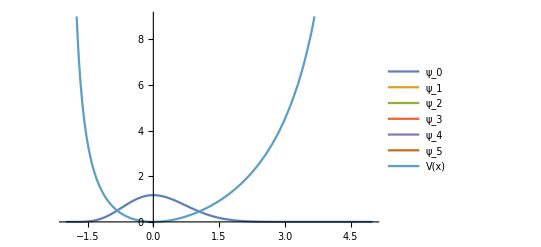

```mathematica
Plot[{Funmod[Ps0[x]/(1.2*10^19)],Funmod[Psi1[x]/(7.5*10^20)]+1.2,Funmod[Psi2[x]/(3.4*10^22)]+2.5,Funmod[Psi3[x]/(1.2*10^24)]+4,Funmod[Psi4[x]/(3.2*10^25)]+5.6,Funmod[Psi5[x]/(1*10^27)]+7.5,V},{x,-2,5},PlotRange->{0,9},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"}]
```

### Asimétrico derecha

#### Parámetros

```mathematica
a = 5;
b = 2;
l = 1;
w = 1;
```

#### Potencial

```mathematica
m=b*a/((a+x)*(b-x));
V = (m*w^2*x^2)/2;
```

#### Constantes de normalización

```mathematica
C0= (a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 *0+2^2 a*b+1)*Gamma[2 *0+2^2 a*b+1]*Factorial[0]/(Gamma[0+2*l^2*(a^2*b/(a+b))+1]*Gamma[0+2*l^2*(a^2*b/(a+b))+1])];
C1 = (a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 1+2^2 a*b+1)*Gamma[2 1+2^2 a*b+1]*Factorial[1]/(Gamma[1+2*l^2*(a^2*b/(a+b))+1]*Gamma[1+2*l^2*(a^2*b/(a+b))+1])];
C2=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 2+2^2 a*b+1)*Gamma[2 2+2^2 a*b+1]*Factorial[2]/(Gamma[2+2*l^2*(a^2*b/(a+b))+1]*Gamma[2+2*l^2*(a^2*b/(a+b))+1])];
C3=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 3+2^2 a*b+1)*Gamma[2 3+2^2 a*b+1]*Factorial[3]/(Gamma[3+2*l^2*(a^2*b/(a+b))+1]*Gamma[3+2*l^2*(a^2*b/(a+b))+1])];
c4=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 4+2^2 a*b+1)*Gamma[2 4+2^2 a*b+1]*Factorial[4]/(Gamma[4+2*l^2*(a^2*b/(a+b))+1]*Gamma[4+2*l^2*(a^2*b/(a+b))+1])];
c5=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 5+2^2 a*b+1)*Gamma[2 5+2^2 a*b+1]*Factorial[5]/(Gamma[5+2*l^2*(a^2*b/(a+b))+1]*Gamma[5+2*l^2*(a^2*b/(a+b))+1])];
```

#### Funciones de onda

```mathematica
Ps0[x_] := C0*(a+x)^(l^2*(a^2*b/(a+b))) *(b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[0,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi1[x_] :=C1*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[1,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi2[x_]:=C2*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[2,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi3[x_]:=C3*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[3,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi4[x_]:=c4*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[4,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi5[x_]:=c5*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[5,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Funmod[p_]:= Abs[p]^2;
```

SetDelayed::write: Tag Times in ((10 ⅇ^(-(50 ⅇ^(9/10 «1»))/(9 (2+Times[«2»]) (5+x))) x)/((2-x) (5+x))-ⅇ^(-(9 x^2)/10-(50 ⅇ^Times[«2»])/(9 Plus[«2»] Plus[«2»])) ((50 ⅇ^(9/10 Power[«2»]))/(9 (2+Times[«2»]) (5+x)^2)-(50 ⅇ^(9/10 Power[«2»]))/(9 (2+Times[«2»])^2 (5+x))-(10 ⅇ^(9/10 Power[«2»]) x)/((2+Times[«2»]) (5+x))))/(2 √5 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√5 x ((10 ⅇ^(-50/9 Power[«1»] «1» Power[«2»]) x)/((2+Times[«2»]) (5+x))-ⅇ^(Times[«2»]+Times[«4»]) (50/9 Power[«2»] Power[«2»] Power[«2»]-«1»-10 «3» Power[«2»])))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«1»])«1»(«1»«1»)/(4 √5 («1»)^(3/2))+(«1»+«1»+«6»)/(2 √5 «1»)))/(2 √10 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/2) x ((√5 x (10 Power[«2»] Power[«2»] x Power[«2»]-Power[«2»] Plus[«1»]))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10«1»«5»«1»«1»]) («1»+«1»)))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«2»]) («1»))/(4 √10 (Power[«2»] «1»)^(3/2))+(«1»)/(2 √10 √(«1» «1»))))/(2 √30 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/6) x ((√(5/2) x (Power[«2»] Power[«2»] x Power[«1»] Power[«2»] Plus[«2»]-«1»))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10 «1») (-1/4 «4»+1/2 «3»)))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«2»]) («1»))/(4 √30 (Power[«2»] «1»)^(3/2))+(«1»)/(2 √30 √(«1» «1»))))/(4 √30 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/6) x ((√(5/6) x (Power[«2»] Power[«2»] x Power[«1»] Power[«2»] Plus[«2»]-«1»))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10 «1») (-1/4 «4»+1/2 «3»)))/(2 (2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«1»]) («1»))/(8 √30 (Power[«2»] «1»)^(3/2))+(-«1» «5»+«8»)/(4 √30 √(«1»))))/(20 √6 √(1/((2-x) (5+x))))[x_] is Protected.

#### Gráficas

General::munfl: Exp[-3.27619×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.41755×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

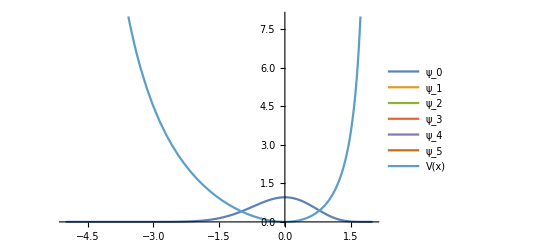

```mathematica
Plot[{Funmod[Ps0[x]/(3*10^10)],Funmod[Psi1[x]/(8*10^11)]+1.1,Funmod[Psi2[x]/(1.5*10^13)]+2.4,Funmod[Psi3[x]/(2.6*10^14)]+3.6,Funmod[Psi4[x]/(4*10^15)]+4.9,Funmod[Psi5[x]/(7*10^16)]+6.5,V},{x,-5,2},PlotRange->{0,8},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"}]
```

### Potencial expandido

#### Parámetros

```mathematica
a = 20;
b = 30;
l = 1;
w = 1;
```

#### Potencial

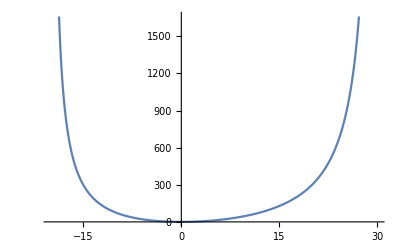

```mathematica
m=b*a/((a+x)*(b-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-a,b}]
```

#### Constantes de normalización

```mathematica
C0= (a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 *0+2^2 a*b+1)*Gamma[2 *0+2^2 a*b+1]*Factorial[0]/(Gamma[0+2*l^2*(a^2*b/(a+b))+1]*Gamma[0+2*l^2*(a^2*b/(a+b))+1])];
C1 = (a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 1+2^2 a*b+1)*Gamma[2 1+2^2 a*b+1]*Factorial[1]/(Gamma[1+2*l^2*(a^2*b/(a+b))+1]*Gamma[1+2*l^2*(a^2*b/(a+b))+1])];
C2=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 2+2^2 a*b+1)*Gamma[2 2+2^2 a*b+1]*Factorial[2]/(Gamma[2+2*l^2*(a^2*b/(a+b))+1]*Gamma[2+2*l^2*(a^2*b/(a+b))+1])];
C3=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 3+2^2 a*b+1)*Gamma[2 3+2^2 a*b+1]*Factorial[3]/(Gamma[3+2*l^2*(a^2*b/(a+b))+1]*Gamma[3+2*l^2*(a^2*b/(a+b))+1])];
c4=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 4+2^2 a*b+1)*Gamma[2 4+2^2 a*b+1]*Factorial[4]/(Gamma[4+2*l^2*(a^2*b/(a+b))+1]*Gamma[4+2*l^2*(a^2*b/(a+b))+1])];
c5=(a+b)^(-l^2*a*b-(1/2))*Sqrt[(2 5+2^2 a*b+1)*Gamma[2 5+2^2 a*b+1]*Factorial[5]/(Gamma[5+2*l^2*(a^2*b/(a+b))+1]*Gamma[5+2*l^2*(a^2*b/(a+b))+1])];
```

#### Funciones de onda

```mathematica
Ps0[x_] := C0*(a+x)^(l^2*(a^2*b/(a+b))) *(b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[0,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi1[x_] :=C1*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[1,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi2[x_]:=C2*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[2,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi3[x_]:=C3*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[3,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi4[x_]:=c4*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[4,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Psi5[x_]:=c5*(a+x)^(l^2*(a^2*b/(a+b))) (b-x)^(l^2*(a*b^2/(a+b)))*JacobiP[5,2*l^2*(a^2*b/(a+b)),2*l^2*(a*b^2/(a+b)),(2x+a-b)/(a+b)];
Funmod[p_]:= Abs[p]^2;
```

SetDelayed::write: Tag Times in ((10 ⅇ^(-(50 ⅇ^(9/10 «1»))/(9 (2+Times[«2»]) (5+x))) x)/((2-x) (5+x))-ⅇ^(-(9 x^2)/10-(50 ⅇ^Times[«2»])/(9 Plus[«2»] Plus[«2»])) ((50 ⅇ^(9/10 Power[«2»]))/(9 (2+Times[«2»]) (5+x)^2)-(50 ⅇ^(9/10 Power[«2»]))/(9 (2+Times[«2»])^2 (5+x))-(10 ⅇ^(9/10 Power[«2»]) x)/((2+Times[«2»]) (5+x))))/(2 √5 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√5 x ((10 ⅇ^(-50/9 Power[«1»] «1» Power[«2»]) x)/((2+Times[«2»]) (5+x))-ⅇ^(Times[«2»]+Times[«4»]) (50/9 Power[«2»] Power[«2»] Power[«2»]-«1»-10 «3» Power[«2»])))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«1»])«1»(«1»«1»)/(4 √5 («1»)^(3/2))+(«1»+«1»+«6»)/(2 √5 «1»)))/(2 √10 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/2) x ((√5 x (10 Power[«2»] Power[«2»] x Power[«2»]-Power[«2»] Plus[«1»]))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10«1»«5»«1»«1»]) («1»+«1»)))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«2»]) («1»))/(4 √10 (Power[«2»] «1»)^(3/2))+(«1»)/(2 √10 √(«1» «1»))))/(2 √30 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/6) x ((√(5/2) x (Power[«2»] Power[«2»] x Power[«1»] Power[«2»] Plus[«2»]-«1»))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10 «1») (-1/4 «4»+1/2 «3»)))/((2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«2»]) («1»))/(4 √30 (Power[«2»] «1»)^(3/2))+(«1»)/(2 √30 √(«1» «1»))))/(4 √30 √(1/((2-x) (5+x))))[x_] is Protected.

SetDelayed::write: Tag Times in ((√(5/6) x ((√(5/6) x (Power[«2»] Power[«2»] x Power[«1»] Power[«2»] Plus[«2»]-«1»))/((2+Times[«2»]) √(Power[«2»] Power[«2»]) (5+x))-ⅇ^(-9/10 «1») (-1/4 «4»+1/2 «3»)))/(2 (2-x) √(1/((2+Times[«2»]) (5+x))) (5+x))-ⅇ^(-(9 x^2)/10) (-((-Power[«2»] Power[«2»]+Power[«2»] Power[«1»]) («1»))/(8 √30 (Power[«2»] «1»)^(3/2))+(-«1» «5»+«8»)/(4 √30 √(«1»))))/(20 √6 √(1/((2-x) (5+x))))[x_] is Protected.

#### Gráficas

General::munfl: 0.00102143^240 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.09586×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

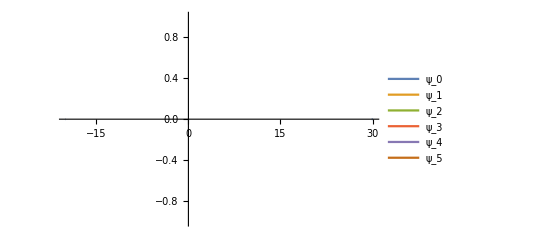

```mathematica
Plot[{Ps0[x],Psi1[x],Psi2[x],Psi3[x],Psi4[x],Psi5[x]},{x,-a,b},PlotRange->All,PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"}]
```

## Trabajo de recuperación

### Recuperación de entero simétrico

#### Parámetros y constantes

```mathematica
a=1;
b=4;
c=4;
h=1;
w=1;
```

#### Masa variable y potencial

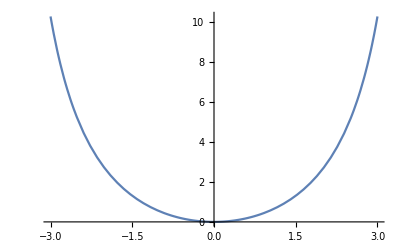

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-3,3}]
```

#### Función general conformable

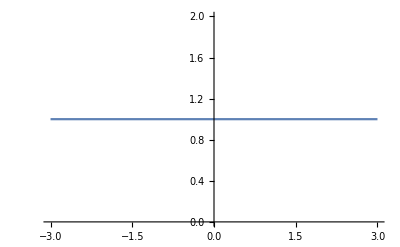

```mathematica
f[x_,a_]:=Exp[-x^2*(1-a)]
Plot[f[x,a],{x,-3,3}]
```

#### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

#### Solución espacial

```mathematica
g=Integrate[x*m/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

#### Gráficas

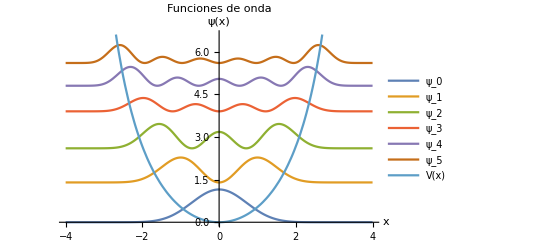

```mathematica
Plot[{Funmod[Psi0/(4*10^9)],Funmod[Psi1/(4*10^9)]+1.4,Funmod[Psi2/(4*10^9)]+2.6,Funmod[Psi3/(4*10^9)]+3.9,Funmod[Psi4/(4*10^9)]*7+4.8,Funmod[Psi5/(4*10^9)]*120+5.6,V},{x,-4,4},PlotRange->{0,6.6},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

### Recuperación de entero asimétrico izquierda

#### Parámetros y constantes

```mathematica
a=1;
b=2;
c=5;
h=1;
w=1;
```

#### Masa variable y potencial

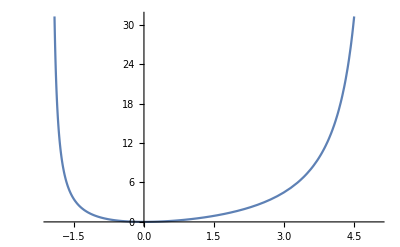

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-b,c}]
```

#### Función general conformable

```mathematica
f[x_,a_]:=Exp[-x^2*(1-a)]
Plot[f[x,a],{x,-3,3}]
```

-Graphics-

#### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

#### Solución espacial

```mathematica
g=Integrate[x*m/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

#### Gráficas

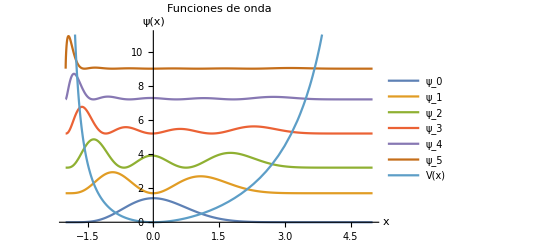

```mathematica
Plot[{Funmod[Psi0/(600000)],Funmod[Psi1/(600000)]+1.7,Funmod[Psi2/(600000)]+3.2,Funmod[Psi3/(600000)]+5.2,Funmod[Psi4/(600000)]*2+7.2,Funmod[Psi5/(600000)]*11+9,V},{x,-2,5},PlotRange->{0,11},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

### Recuperación de entero asimétrico derecha

#### Parámetros y constantes

```mathematica
a=1;
b=5;
c=2;
h=1;
w=1;
```

#### Masa variable y potencial

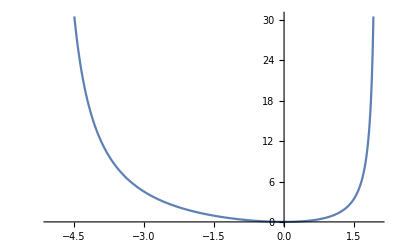

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-b,c}]
```

#### Función general conformable

```mathematica
f[x_,a_]:=Exp[-x^2*(1-a)]
Plot[f[x,a],{x,-3,3}]
```

-Graphics-

#### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

#### Solución espacial

```mathematica
g=Integrate[x*m/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

#### Gráficas

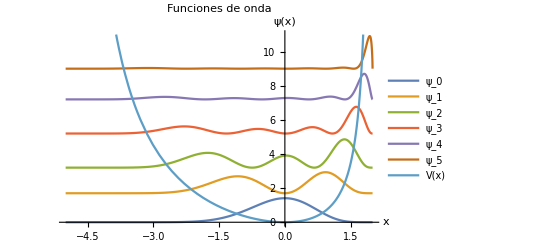

```mathematica
Plot[{Funmod[Psi0/(600000)],Funmod[Psi1/(600000)]+1.7,Funmod[Psi2/(600000)]+3.2,Funmod[Psi3/(600000)]+5.2,Funmod[Psi4/(600000)]*2+7.2,Funmod[Psi5/(600000)]*11+9,V},{x,-5,2},PlotRange->{0,11},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

## Orden de derivación fraccional

## Función exponencial

### Orden de derivación 1/2

#### fraccional simétrico

##### Parámetros y constantes

```mathematica
a=1/2;
b=4;
c=4;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-3,3}]
```

-Graphics-

##### Función general conformable

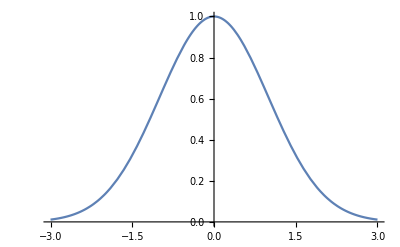

```mathematica
f[x_,a_]:=Exp[-x^2*(1-a)]
Plot[f[x,a],{x,-3,3}]
```

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x*m/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

##### Gráficas

General::munfl: Exp[-161122.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

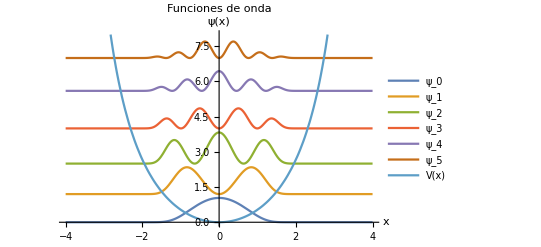

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+1.2,Funmod[Psi2/(0.25)]+2.5,Funmod[Psi3/(0.2)]+4,Funmod[Psi4/(0.09)]+5.6,Funmod[Psi5/(0.02)]+7, V},{x,-4,4},PlotRange->{0,8},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

#### fraccional asimétrico izquierda

##### Parámetros y constantes

```mathematica
a=1/2;
b=2;
c=5;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-b,c}]
```

-Graphics-

##### Función general conformable

```mathematica
f[x_,a_]:=Exp[-x^2*(1-a)]
Plot[f[x,a],{x,-3,3}]
```

-Graphics-

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w*m/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w*m/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

Integrate::idiv: Integral of ⅇ^((20 ⅇ^(x^2/2))/((-5+x) (2+x))) does not converge on {-5,2}.

##### Gráficas

General::munfl: Exp[-73797.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73799.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

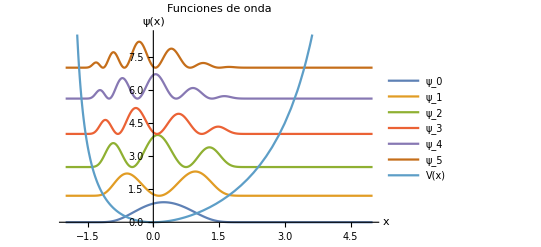

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+1.2,Funmod[Psi2/(0.25)]+2.5,Funmod[Psi3/(0.2)]+4,Funmod[Psi4/(0.09)]+5.6,Funmod[Psi5/(0.02)]+7,V},{x,-2,5},PlotRange->{0,8.5},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

#### fraccional asimétrico derecha

##### Parámetros y constantes

```mathematica
a=1/2;
b=5;
c=2;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-b,c}]
```

-Graphics-

##### Función general conformable

```mathematica
f[x_,a_]:=Exp[-x^2*(1-a)]
Plot[f[x,a],{x,-3,3}]
```

-Graphics-

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w*m/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w*m/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

Integrate::idiv: Integral of ⅇ^((20 ⅇ^(x^2/2))/((-2+x) (5+x))) does not converge on {-2,5}.

##### Gráficas

General::munfl: Exp[-2.67883×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

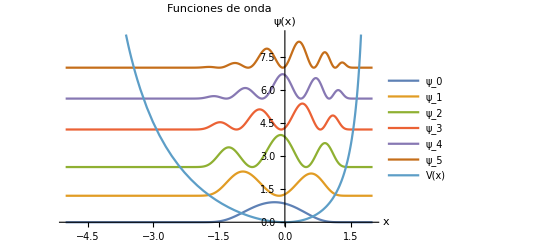

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+1.2,Funmod[Psi2/(0.25)]+2.5,Funmod[Psi3/(0.2)]+4.2,Funmod[Psi4/(0.09)]+5.6,Funmod[Psi5/(0.02)]+7,V},{x,-5,2},PlotRange->{0,8.5},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

### Orden de derivación 1/10

#### fraccional simétrico

##### Parámetros y constantes

```mathematica
a=1/10;
b=4;
c=4;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-3,3}]
```

-Graphics-

##### Función general conformable

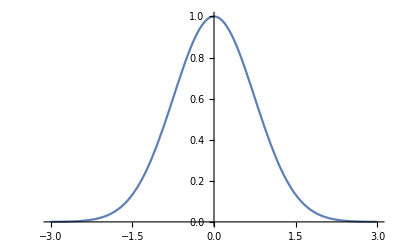

```mathematica
f[x_,a_]:=Exp[-x^2*(1-a)]
Plot[f[x,a],{x,-3,3}]
```

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x*m/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

##### Gráficas

General::munfl: Exp[-8.85417×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

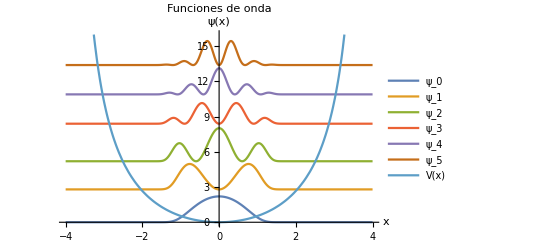

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+2.8,Funmod[Psi2/(0.25)]+5.2,Funmod[Psi3/(0.2)]+8.4,Funmod[Psi4/(0.09)]+10.9,Funmod[Psi5/(0.02)]+13.4, V},{x,-4,4},PlotRange->{0,16},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

#### fraccional asimétrico izquierda

##### Parámetros y constantes

```mathematica
a=1/10;
b=2;
c=5;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-b,c}]
```

-Graphics-

##### Función general conformable

```mathematica
f[x_,a_]:=Exp[-x^2*(1-a)]
Plot[f[x,a],{x,-3,3}]
```

-Graphics-

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w*m/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w*m/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

Integrate::idiv: Integral of ⅇ^((100 ⅇ^((9 x^2)/10))/(9 (-5+x) (2+x))) does not converge on {-5,2}.

##### Gráficas

General::munfl: Exp[-203020.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-203024.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

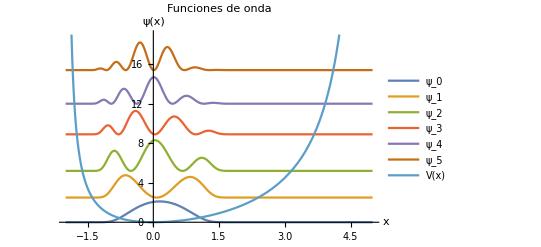

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+2.5,Funmod[Psi2/(0.25)]+5.2,Funmod[Psi3/(0.2)]+8.9,Funmod[Psi4/(0.09)]+12,Funmod[Psi5/(0.02)]+15.4, V},{x,-2,5},PlotRange->{0,19},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

#### fraccional asimétrico derecha

##### Parámetros y constantes

```mathematica
a=1/10;
b=5;
c=2;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-b,c}]
```

-Graphics-

##### Función general conformable

```mathematica
f[x_,a_]:=Exp[-x^2*(1-a)]
Plot[f[x,a],{x,-3,3}]
```

-Graphics-

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w*m/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w*m/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

Integrate::idiv: Integral of ⅇ^((100 ⅇ^((9 x^2)/10))/(9 (-2+x) (5+x))) does not converge on {-2,5}.

##### Gráficas

General::munfl: Exp[-3.27619×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

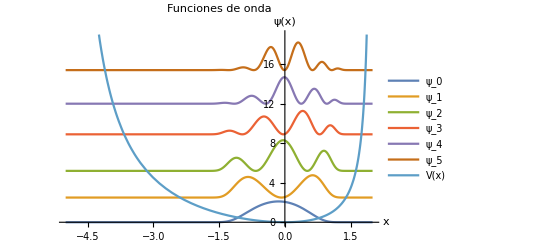

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+2.5,Funmod[Psi2/(0.25)]+5.2,Funmod[Psi3/(0.2)]+8.9,Funmod[Psi4/(0.09)]+12,Funmod[Psi5/(0.02)]+15.4, V},{x,-5,2},PlotRange->{0,19},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

## Función cosenoidal

### Orden de derivación 1/2

#### fraccional simétrico

##### Parámetros y constantes

```mathematica
a=1/2;
b=5;
c=5;
h=1;
w=1;
```

##### Masa variable y potencial

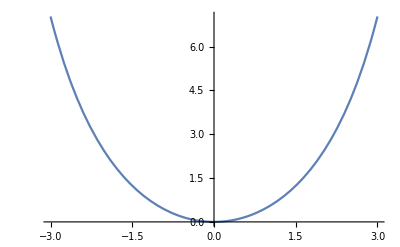

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-3,3}]
```

##### Función general conformable

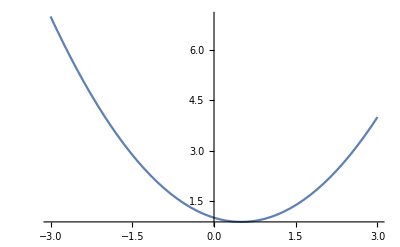

```mathematica
f[x_,a_]:=(1-a)*x^2-(1-a)x+1;
Plot[f[x,a],{x,-3,3}]
```

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x*m/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

##### Gráficas

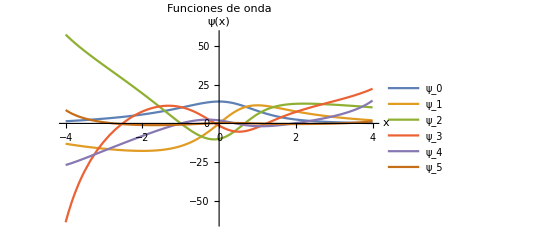

```mathematica
Plot[{Psi0,Psi1,Psi2,Psi3,Psi4,Psi5},{x,-10,10},PlotRange->All,PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}
```

#### fraccional asimétrico izquierda

##### Parámetros y constantes

```mathematica
a=1/2;
b=2;
c=5;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-b,c}]
```

-Graphics-

##### Función general conformable

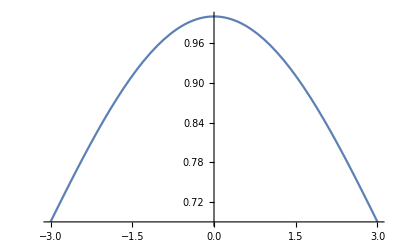

```mathematica
f[x_,a_]:=(Cos[x*(1-a)]+2)/3;
Plot[f[x,a],{x,-3,3}]
```

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w*m/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w*m/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

Integrate::idiv: Integral of ⅇ^((20 ⅇ^(x^2/2))/((-5+x) (2+x))) does not converge on {-5,2}.

##### Gráficas

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+1.2,Funmod[Psi2/(0.25)]+2.5,Funmod[Psi3/(0.2)]+4,Funmod[Psi4/(0.09)]+5.6,Funmod[Psi5/(0.02)]+7,V},{x,-2,5},PlotRange->{0,8.5},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

General::munfl: Exp[-73797.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73799.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

#### fraccional asimétrico derecha

##### Parámetros y constantes

```mathematica
a=1/2;
b=5;
c=2;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-b,c}]
```

-Graphics-

##### Función general conformable

```mathematica
f[x_,a_]:=(Cos[x*(1-a)]+2)/3;
Plot[f[x,a],{x,-3,3}]
```

-Graphics-

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w*m/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w*m/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

Integrate::idiv: Integral of ⅇ^((20 ⅇ^(x^2/2))/((-2+x) (5+x))) does not converge on {-2,5}.

##### Gráficas

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+1.2,Funmod[Psi2/(0.25)]+2.5,Funmod[Psi3/(0.2)]+4.2,Funmod[Psi4/(0.09)]+5.6,Funmod[Psi5/(0.02)]+7,V},{x,-5,2},PlotRange->{0,8.5},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

General::munfl: Exp[-2.67883×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

### Orden de derivación 1/10

#### fraccional simétrico

##### Parámetros y constantes

```mathematica
a=1/10;
b=4;
c=4;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-3,3}]
```

-Graphics-

##### Función general conformable

```mathematica
f[x_,a_]:=(Cos[x*(1-a)]+2)/3;
Plot[f[x,a],{x,-3,3}]
```

-Graphics-

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x*m/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

##### Gráficas

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+2.8,Funmod[Psi2/(0.25)]+5.2,Funmod[Psi3/(0.2)]+8.4,Funmod[Psi4/(0.09)]+10.9,Funmod[Psi5/(0.02)]+13.4, V},{x,-4,4},PlotRange->{0,16},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

General::munfl: Exp[-8.85417×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

#### fraccional asimétrico izquierda

##### Parámetros y constantes

```mathematica
a=1/10;
b=2;
c=5;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-b,c}]
```

-Graphics-

##### Función general conformable

```mathematica
f[x_,a_]:=(Cos[x*(1-a)]+2)/3;
Plot[f[x,a],{x,-3,3}]
```

-Graphics-

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w*m/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w*m/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

Integrate::idiv: Integral of ⅇ^((100 ⅇ^((9 x^2)/10))/(9 (-5+x) (2+x))) does not converge on {-5,2}.

##### Gráficas

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+2.5,Funmod[Psi2/(0.25)]+5.2,Funmod[Psi3/(0.2)]+8.9,Funmod[Psi4/(0.09)]+12,Funmod[Psi5/(0.02)]+15.4, V},{x,-2,5},PlotRange->{0,19},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

-Graphics-

#### fraccional asimétrico derecha

##### Parámetros y constantes

```mathematica
a=1/10;
b=5;
c=2;
h=1;
w=1;
```

##### Masa variable y potencial

```mathematica
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-b,c}]
```

-Graphics-

##### Función general conformable

```mathematica
f[x_,a_]:=(Cos[x*(1-a)]+2)/3;
Plot[f[x,a],{x,-3,3}]
```

-Graphics-

##### Solución temporal

```mathematica
phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];
```

##### Solución espacial

```mathematica
g=Integrate[x/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w*m/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w*m/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
Funmod[p_]:= Abs[p]^2;
```

Integrate::idiv: Integral of ⅇ^((100 ⅇ^((9 x^2)/10))/(9 (-2+x) (5+x))) does not converge on {-2,5}.

##### Gráficas

```mathematica
Plot[{Funmod[Psi0/(0.4)],Funmod[Psi1/(0.3)]+2.5,Funmod[Psi2/(0.25)]+5.2,Funmod[Psi3/(0.2)]+8.9,Funmod[Psi4/(0.09)]+12,Funmod[Psi5/(0.02)]+15.4, V},{x,-5,2},PlotRange->{0,19},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","ψ(x)"}]
```

General::munfl: Exp[-3.27619×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-